```mathematica
Mathods of Mathematical Physics
Lihong Ao
2019271014
SZU,physics
```

```mathematica
exersice 1-1
```

```mathematica
|z-Subscript[z, 0]|≤R,k a+b≤0
z=a+b ⅈ,Subscript[z, 0]=Subscript[a, 0]+Subscript[b, 0] ⅈ,k Subscript[a, 0]+Subscript[b, 0]=0
```

```mathematica
|z|+Re z≤1
```

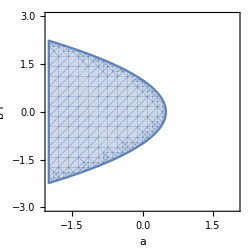

```mathematica
RegionPlot[x+√(y^2+x^2)≤1,{x,-2,2},{y,-3,3},ImageSize->250,AxesLabel->{a,"b i"}]
```

```mathematica
z=(1-2 ⅈ)/(3-4 ⅈ)-(2-ⅈ)/(5ⅈ)=16/25+(8 ⅈ)/25
Re z=16/25,Im z=8/25,|z|=8/(5 √5),arg z=ArcTan 1/2
```

```mathematica
(√3-ⅈ)^5=(ⅇ^(-π/6 ⅈ))^5=ⅇ^((-5π)/6 ⅈ)
```

```mathematica
z^2-(2+3ⅈ)z-1+3ⅈ=((-1-ⅈ)+z) ((-1-2 ⅈ)+z)=0
z=1+ⅈ or 1+2ⅈ
```

```mathematica
z^2-(2+3ⅈ)z-1+3ⅈ//FullSimplify
```

((-1-ⅈ)+z) ((-1-2 ⅈ)+z)

```mathematica
exersice 1-2
```

```mathematica
z=x+ⅈ y
|z-2ⅈ|=|z+2|->x^2+(y-2)^2=(x+2)^2+y^2->-4 (x+y)=0
```

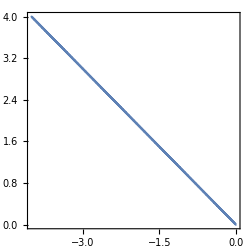

```mathematica
RegionPlot[x^2+(y-2)^2==(x+2)^2+y^2,{x,-4,0},{y,0,4},ImageSize->250]
```

```mathematica
f(z)=1/(2ⅈ)(z/(z̄)-(z̄)/z)=1/(2ⅈ)((x+ⅈ y)/(x-ⅈ y)-(x-ⅈ y)/(x+ⅈ y))=(2 x y)/(x^2+y^2)=(2 y/x)/((y/x)^2+1)
y/x=k->lim_(z->0) f(z)=(2k)/(k^2+1)≠const
```

```mathematica
Plot3D[(2 x y)/(x^2+y^2),{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
w=|z|^2=x^2+y^2⇒u=x^2+y^2,v=0
(∂u)/(∂x)≠(∂v)/(∂y)
```

```mathematica
u=2(x-1)y,f(2)=-i
(*x=(z+z^-)/2,y=(z-z^-)/(2i)⇒u=2((z+z^-)/2-1)(z-z^-)/(2i)=1/2(z^2/(2i)-z/i+ ((z^-)^2)/(2i)-z^-/i)=1/2(z^2/(2i)-z/i+ ((z^-)^2)/(2i)-z^-/i)
f(z)=z^2/(2i)+z/i+C
f(2)=-i⇒f(z)=z^2/(2i)+z/i+i*)
ⅆv=(∂v)/(∂x)ⅆx+(∂v)/(∂y)ⅆy=-(∂u)/(∂y)ⅆx+(∂u)/(∂x)ⅆy=2y ⅆy-(2x-2)ⅆx
⟹v=y^2-x^2+2x+c=-z^2+z+z̄+c
f(2)=-i,f(z)=u+i v=-i+2 z-(3 z^2)/2+(z̄)^2/2
```

```mathematica
v=y/(x^2+y^2),f(2)=0
v=((z-z^-)/(2i))/(((z+z^-)/2)^2+((z-z^-)/(2i))^2)=1/(2i)(z-z^-)/(z z^-)=1/(2i)(-1/z--1/z^-)
f(z)=-1/z+C
f(2)=0⇒f(z)=-1/z+1/2
```

```mathematica
u=x y^2⇒(∂u)/(∂x)=y^2,(∂u)/(∂y)=2 x y
ⅆv=(∂v)/(∂x)ⅆx+(∂v)/(∂y)ⅆy=-(∂u)/(∂y)ⅆx+(∂u)/(∂x)ⅆy=-y^2 ⅆx+2 x yⅆy
(∂v)/(∂x)=-y^2,(∂v)/(∂y)=2 x y
```

```mathematica
v(x,y)=x^3-3 y^2 x
(∂^2 v)/(∂x^2)+(∂^2 v)/(∂y^2)=6x-6x=0
v=(f(z)-f(z^-))/(2i)=((z+z^-)/2)^3-3((z-z^-)/(2i))^2(z+z^-)/2=1/(2i) (i z^3-OverBar[i z^3])
f(z)=i z^3
```

```mathematica
z=x+ⅈ y
Sin z=(ⅇ^(ⅈ z)-ⅇ^(-ⅈ z))/(2ⅈ)=1/(2ⅈ)(ⅇ^y(Cos x+ⅈ Sin x)+ⅇ^-y(Cos x-ⅈ Sin x)),
Cosh y=(ⅇ^y+ⅇ^-y)/2,Sinh y=(ⅇ^y-ⅇ^-y)/2
Sin x Cosh y-ⅈ Sin x Sinh y=Sin z
```

```mathematica
ⅇ^z=1+ⅈ √3
⟺ z=Ln(1+ⅈ √3)=ln 2+ⅈ (π/3+2k π)  (k∈ℤ)
```

```mathematica
(1+ⅈ)^ⅈ=ⅇ^(ⅈ Ln(1+ⅈ))=ⅇ^(ⅈ(ln √2+ⅈ(π/4+2k π)))=ⅇ^(ⅈ ln √2-π/4-2k π)
```

```mathematica
w=1/z=1/(x+ⅈ y)=x/(x^2-y^2)+(-ⅈ y)/(x^2-y^2)
x^2+y^2=4 ⟹  η=(√(4-y^2))/(4-2 y^2),ξ=(-ⅈ y)/(4-2 y^2) ⟹ ξ=(η^2 √(32+(2 (1±√(1+32 η^2)))/η^2))/(±1+√(1+32 η^2))
x=1 ⟹ η=1/(1-y^2),ξ=(ⅈ y)/(1-y^2) ⟹ ξ=+±ⅈ √((η-1)η)
```

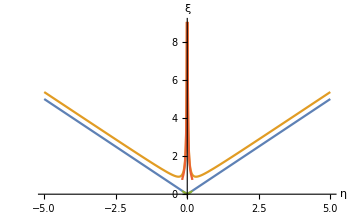

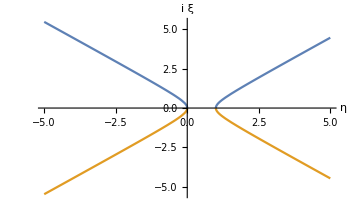

```mathematica
Plot[{(η^2 √(32+(2 (1+√(1+32 η^2)))/η^2))/(+1+√(1+32 η^2)),(η^2 √(32+(2 (1+√(1+32 η^2)))/η^2))/(-1+√(1+32 η^2)),(η^2 √(32+(2 (1+√(1-32 η^2)))/η^2))/(+1+√(1+32 η^2)),(η^2 √(32+(2 (1+√(1-32 η^2)))/η^2))/(-1+√(1+32 η^2))},{η,-5,5},ImageSize->350,AxesLabel->{η,ξ}]
Plot[{√((η-1)η),-√((η-1)η)},{η,-5,5},ImageSize->350,AxesLabel->{η,i ξ}]
```

```mathematica
exersice 2.1-2.3
```

```mathematica
l:(0,1+ⅈ)
∫_l (x-y+ⅈ x^2)ⅆz=∫_l (x-y+ⅈ x^2)ⅆ(x+ⅈy)=∫_l (x-y+ⅈ x^2)ⅆx+ⅈ∫_l (x-y+ⅈ x^2)ⅆy
t=x=y
∫_0^1 ⅈ t^2 ⅆt+ⅈ∫_0^1 ⅈ t^2 ⅆt=-1/3+ⅈ/3
```

```mathematica
|∫_-ⅈ^ⅈ (x^2+ⅈ y^2)ⅆz|≤∫_-ⅈ^ⅈ|x^2+ⅈ y^2|ⅆs=∫_-ⅈ^ⅈ |1+(ⅈ-1)y^2|ⅆs=∫_-π^π |1+(ⅈ-1)Sin^2 θ|ⅆθ
Re(1+(ⅈ-1)Sin^2 θ)>0,Im(1+(ⅈ-1)Sin^2 θ)>0
∫_-π^π |1+(ⅈ-1)Sin^2 θ|ⅆθ=2∫_0^π (1+(ⅈ-1)Sin^2 θ)ⅆθ=(1+ⅈ) π
```

```mathematica
l(a)<0,l(b)<0:
∮_l 1/((z-a)(z-b))ⅆz =2π ⅈ(Res f(a)+Res f(b))=2π ⅈ(1/(a-b)+1/(b-a))=0
```

```mathematica
∫_1^(1+(π ⅈ)/2) z ⅇ^z ⅆz=∫z ⅇ^z ⅆz(|_1)^(1+(π ⅈ)/2)=-(ⅇ π)/2
```

```mathematica
∮_l (2 z^2-z+1)/(z-1)ⅆz    |z|=2        z=1:
f(z)=2 z^2-z+1
∮_l (2 z^2-z+1)/(z-1)ⅆz =2π ⅈ f(1)=4π ⅈ
```

```mathematica
l(3ⅈ)<0,l(-3ⅈ)>0:
∫_l 1/(z^2+9)ⅆz=∫_l (f(z))/(z+3ⅈ)ⅆz,f(z)=1/(z-3ⅈ)
∫_l 1/(z^2+9)ⅆz=2π ⅈ f(-3ⅈ)=-π/3
```

```mathematica
∮_l (Cos π z)/(z-1)^5 ⅆz=(2π ⅈ)/(4!)(Cos π z)^(4)|_(z=1)=-(π^5 ⅈ)/12
```

```mathematica
∮_l (z-Sin z)/z^6 ⅆz=(2π ⅈ)/(5!)(z-Sin z)^(5)|_(z=0)=-(2π ⅈ)/(5!)
```

```mathematica
l(0)<0,l(1)>0:
1/(2π ⅈ)∮_l ⅇ^z/(z(1-z)^3)ⅆz=1/(2π ⅈ)(2π ⅈ ⅇ^z/(1-z)^3|_(z=0))=1
```

```mathematica
exersice 3.2-3.5
```

```mathematica
Subscript[a, k]=k/2^k
R=Underscript[Lim, k->∞]|Subscript[a, k]/Subscript[a, k+1]|=Underscript[Lim, k->∞](2k)/(k+1)=2
```

```mathematica
R=Underscript[Lim, k->∞]|Subscript[a, k]/Subscript[a, k+1]|=Underscript[Lim, k->∞](1+1/k)^k=ⅇ
```

```mathematica
Underscript[Lim, k->∞]|Subscript[a, k]/Subscript[a, k+1]|=R
Underscript[Lim, k->∞]|Subscript[a, k]^n/Subscript[a, k+1]^n|=Underscript[Lim, k->∞]|Subscript[a, k]/Subscript[a, k+1]|^n=(Underscript[Lim, k->∞]|Subscript[a, k]/Subscript[a, k+1]|)^n=R^n
```

```mathematica
1/((z^2+1)^2)=1/((z-ⅈ+2ⅈ)^2(z-ⅈ)^2)=^(z-ⅈ=w)1/w^2 1/(w+2ⅈ)^2
1/(w+2ⅈ)=-ⅈ/2+w/4+(ⅈ w^2)/8-w^3/16+…+ⅈ^(n+3)w^n/2^n+…
1/(w+2ⅈ)^2=-1/4-(ⅈ w)/4+(3 w^2)/16+(ⅈ w^3)/8+…+ⅈ^(n+2)((n+1) w^n)/2^n+…
1/((z^2+1)^2)=∑_(n=0)^∞ ⅈ^(n+2)((n+1) w^(n-2))/2^n
```

```mathematica
0< |a|< |b|⟹  1/((z-a)(z-b))=1/(b-a)(1/(z-a)-1/(z-b))
z=0: 1/(b-a)(1/(z-a)-1/(z-b))=1/(b-a)(1/a 1/(z/a-1)-1/b 1/(z/b-1))=1/(b-a)(1/b+z/b^2+z^2/b^3+…-1/a+z/a^2+z^2/a^3+…)
z=a: 1/(b-a)(1/(z-a)-1/(z-b))=1/(b-a)(1/(z-a)-1/(z-a+a-b))=1/(b-a)(1/(z-a)-1/(b-a)1/((z-a)/(b-a)-1))=(z-a)^-1/(b-a)-1/(b-a)^2-(z-a)/(b-a)^3-(z-a)^2/(b-a)^4-…
{z:|a|<|z|<|b|}:
 1/(b-a)(1/(z-a)-1/(z-b))=1/(b-a)(1/z 1/(1-a/z)+1/b 1/(1-z/b))=1/(b-a)(1/z+a/z^2+a^2/z^3+…+1/b+z/b^2+z^2/b^3+…)
```

```mathematica
f(z)=1/(z(1-z))=1/z+1/(1-z)
{z:|z+1|<1}: 
f(z)=1/(z+1-1)+1/2 1/(1-(z+1)/2)=1/2(1+(z+1)/2+((z+1)/2)^2+…)-1-(z+1)-(z+1)^2-…=-∑_(n=0)^∞ ((2^(n+1)-1)(z+1)^n)/2^(n+1)
{z:1<|z+1|<2}:
f(z)=1/(z+1)1/(1-1/(z+1))+1/2 1/(1-(z+1)/2)=1/2(1+(z+1)/2+((z+1)/2)^2+…)+1/(z+1)+1+(z+1)+(z+1)^2+…=-∑_(n=0)^∞ ((2^(n+1)-1)(z+1)^n)/2^(n+1)
```

```mathematica
f(z)=(z-1)/(z(z^2+4)^2)=(z-1)/(z(z+2ⅈ)^2(z-2ⅈ)^2)    z=0,z=-2ⅈ,z=2ⅈ
ⅆ/ⅆz z f(z)|_(z=0)=ⅆ/ⅆz(z-1)/((z^2+4)^2)|_(z=0)=1/16≠0
```

```mathematica
f(z)=z/(z+1)=1-1/(z+1)    z=-1
```

```mathematica
f(z)=(1-Cos z)/z^4=(1-(1-z^2/(2!)+z^4/(4!)-z^6/(6!)+…))/z^4=z^-2/(2!)-1/(4!)+z^2/(6!)-…
Underscript[Lim, n->∞] z^2/(n!)=0           z=∞
```

```mathematica
exersice 5
```

```mathematica
f(z)=z/((z-1)(z+1)^2)
Res(f(z),1)=z/(z+1)^2|_(z=1)=1/4
Res(f(z),-1)=ⅆ/ⅆz z/(z-1)|_(z=-1)=-1/4
Res(f(z),∞)=-(Res(f(z),1)+Res(f(z),-1))=0
```

```mathematica
f(z)=ⅇ^(1/(z-1))=1+1/(1!)1/(z-1)+1/(2!)1/(z-1)^2+……
Res(f(z),1)=1
Res(f(z),∞)=0
```

```mathematica
f(z)=z^(2m)/(1+z)^m   (m∈SubPlus[ℕ])
Res(f(z),-1)=ⅆ^(m-1)/(ⅆ z^(m-1))z^(2m)|_(z=-1)=((2m)!)/((m+1)!)(-1)^(m+1)
Underscript[Lim, z->∞] f(z)=Underscript[Lim, z->∞](z/(z+1))^m z^m=z^m ⟹
 m=1: Res(f(z),∞)=1,m≠1:Res(f(z),∞)=0
```

```mathematica
f(z)=ⅇ^z/(z^2(z^2+9))=ⅇ^z/(z^2(z+3ⅈ)(z-3ⅈ))=1/z^4(1+z+z^2/(2!)+z^3/(3!)+…)(z^2/9-z^4/9^2+z^6/9^3-…)
Res(f(z),0)=ⅆ/ⅆz ⅇ^z/(z^2+9)|_(z=0)=1/9
Res(f(z),-3ⅈ)=ⅇ^z/(z^2(z-3ⅈ))|_(z=-3ⅈ)=-1/54 ⅈ ⅇ^(-3 ⅈ)
Res(f(z),3ⅈ)=ⅇ^z/(z^2(z+3ⅈ))|_(z=3ⅈ)=1/54 ⅈ ⅇ^(3 ⅈ)
Res(f(z),∞)=1/54-1/81=1/162
```

```mathematica
∮_l 1/(z^4+1)ⅆz=∮_l 1/((z-(1+ⅈ)/(√2))(z+(1+ⅈ)/(√2))(z-(1-ⅈ)/(√2))(z+(1-ⅈ)/(√2)))ⅆz=2π ⅈ∑_Subscript[z, 0] Res(1/(Subscript[z, 0]^4+1))(Subscript[z, 0]∈Subscript[Ω, l])
=2π ⅈ(-(1/4+ⅈ/4)/(√2)-(1/4-ⅈ/4)/(√2))=-(π ⅈ)/(√2)
```

```mathematica
f(z)=1/((z-3)(z^5-1))
∮_l f(z)ⅆz=2π ⅈ∑_Subscript[z, 0] Res(f(Subscript[z, 0]))=-2π ⅈ Res(f(z),∞)
f(z)=1/z^6(-z/3-z^2/9-z^3/27-…)(-z^5-z^10-z^15-…)  ⟹ Res(f(z),∞)=1/9
∮_l f(z)ⅆz=(-2π ⅈ)/9
```

```mathematica
f(x)=(1+x^2)/(1+x^4)   Underscript[Lim, x->∞] x f(x)=Underscript[Lim, x->∞] x/(1+x^4)+Underscript[Lim, x->∞] x^3/(1+x^4)=0
∫_(-∞)^∞ f(x)ⅆx=∮_l f(z)ⅆz=2π ⅈ((1/4+ⅈ/4)/(√2)-(1/4+ⅈ/4)/(√2))=0
```

```mathematica
f(x)=(Cos a x)/(1+x^4)(a>0)   0≤Underscript[Lim, x->∞] |x f(x)|≤Underscript[Lim, x->∞] |x/(1+x^4)|=0  ⟹ Underscript[Lim, x->∞] x f(x)=0
∫_0^∞ f(x)ⅆx=∮_l f(z)ⅆz-Re(∫_(Re z=0) f(z)ⅆz)=2π ⅈ(-(-1)^(1/4)/4 Cos((-1)^(1/4) a))=-(-1)^(3/4)/2 π Cos((-1)^(1/4) a)
```

```mathematica
f(x)=(x Sin b x)/(x^2+a^2)=g(x)Sin b x(a>0,b>0)   Underscript[Lim, x->∞] g(x)=0
∫_0^∞ g(x)Sin b xⅆx=π ⅈ ∑_k Res Subscript[(f(Subscript[z, 0])ⅇ^(ⅈ b Subscript[z, 0])), Im z>0]=1/2 ⅈ Sinh(a b)
```

```mathematica
(|b|<1) ∫_0^(2π) 1/(1-2b Cos θ+b^2)ⅆθ=∫_(|z|<1) 1/(1-2b (z+z^-1)/2+b^2)=-ⅈ ∫_(|z|<1) z^2/((-b+z) (-1+b z))ⅆz=2π Res(z^2/((-b+z) (-1+b z)),b)=2π b^2/(b^2-1)
```

```mathematica
∫_0^(2π) 1/(1+Cos^2 θ)ⅆθ=∫_(|z|<1) 1/(1+((z+z^-1)/2)^2)ⅆz/(ⅈ z)=-4 ⅈ∫_(|z|<1) z/((z-ⅈ √(3-2 √2))(z+ⅈ √(3-2 √2))(z-ⅈ √(3+2 √2))(z+ⅈ √(3+2 √2)))ⅆz=8π(1/(8 √2)+1/(8 √2))=√2 π
```

```mathematica
f(x)=1/(x(x+1)(x^2+1))
∫_(-∞)^∞ f(x)ⅆx=∫_C f(z)ⅆz=2π ⅈ Res(f(i))-π ⅈ (Res(f(0))+Res(f(-1)))=(-1/2-ⅈ) π
```

```mathematica
f(x)=(Sin x)/(x(x^2+1)^2)
∫_0^∞ f(x)ⅆx=∫_C f(z)ⅆz=2π ⅈ Res(f(i))-π ⅈ Res(f(0))=π (-Cosh[1]/2+Sinh[1])
```

```mathematica
exercise8
```

```mathematica
1.
(∂^2 u)/(∂t^2)=a(∂^2 u)/(∂x^2),u(0,t)=0,u(l,t)=0,u(x,0)=0,(∂u)/(∂t)(x,0)=I/ρ δ(x-Subscript[x, 0])
u=T(t)X(x) ⟹ T''/T=a X''/X=-λ ⟹ T''+λ T=0,X''+λ/a X=0
λ=0  ⟹ X=0      λ≠0
X=Subscript[c, 1] Cos(√(λ/a)x)+Subscript[c, 2] Sin(√(λ/a)x)
Subscript[X, n]=Subscript[c, n] Sin((n π)/l x) (n∈SubPlus[ℕ])          λ/a=((n π)/l)^2
T=c Cos(√λ t)+d Sin(√λ t)=Subscript[c, n] Cos((n π √a)/l t)+Subscript[d, n] Sin((n π √a)/l t)
u=X T=∑_n Subscript[X, n] Subscript[T, n]=∑_n (Subscript[c, n] Cos((n π √a)/l t)+Subscript[d, n] Sin((n π √a)/l t))Sin((n π)/l x)
∑_n Subscript[c, n] Sin((n π)/l x)=0 ⟹ Subscript[c, n]=0
∑_n Subscript[d, n](n π √a)/l Sin((n π)/l x)=I/ρ δ(x-Subscript[x, 0]) ⟹ Subscript[d, n]=1/(n π √a)∫_0^l I/ρ δ(x-Subscript[x, 0])Sin((n π)/l x)ⅆx=I/(ρ n π √a)Sin((n π)/l Subscript[x, 0])
```

```mathematica
2.
(∂^2 u)/(∂t^2)=a(∂^2 u)/(∂x^2),u(0,t)=0,(∂u)/(∂x)(l,t)=0,u(x,0)=0,(∂u)/(∂t)(x,0)=Subscript[v, 0] δ(x-l)
Subscript[X, n]=Subscript[c, n] Sin(((n+1/2) π)/l x) (n∈SubPlus[ℕ])
u=X T=∑_n Subscript[X, n] Subscript[T, n]=∑_n (Subscript[c, n] Cos((n π √a)/l t)+Subscript[d, n] Sin((n π √a)/l t))Sin(((n+1/2) π)/l x)
∑_n Subscript[c, n] Sin((n π)/l x)=0 ⟹ Subscript[c, n]=0
∑_n Subscript[d, n](n π √a)/l Sin(((n+1/2) π)/l x)=Subscript[v, 0] δ(x-l) ⟹ Subscript[d, n]=1/(n π √a)∫_0^l Subscript[v, 0] δ(x-l)Sin(((n+1/2) π)/l x)ⅆx=Subscript[v, 0]/(n π √a)Sin((n+1/2) π)
```

```mathematica
3.
(∂u)/(∂t)=a(∂^2 u)/(∂x^2),u(0,t)=0,(∂u)/(∂x)(l,t)=0,u(x,0)=φ(x)
u=T(t)X(x) ⟹ T'/T=a X''/X=-λ ⟹ T'+λ T=0,X''+λ/a X=0
λ=0  ⟹ X=0      λ≠0
X=Subscript[c, 1] Cos(√(λ/a)x)+Subscript[c, 2] Sin(√(λ/a)x)
Subscript[X, n]=Subscript[c, n] Sin((n π)/l x) (n∈SubPlus[ℕ])          λ/a=((n π)/l)^2
T=Subscript[c, t] ⅇ^(-λ t)=∑_n Subscript[c, n] ⅇ^(-(n^2 π^2 a)/l^2 t)
u=X T=∑_n Subscript[X, n] Subscript[T, n]=∑_n Subscript[c, n] Sin((n π)/l x)ⅇ^(-(n^2 π^2 a)/l^2 t)     ∑_n Subscript[c, n] Sin((n π)/l x)=φ(x) ⟹ Subscript[c, n]=1/l∫_0^l φ(x)Sin((n π)/l x)ⅆx
```

```mathematica
DSolve[{D[D[u[x,t], x], x]==a D[u[x,t], t],u[x,0]==0,u[0,t]==Subscript[T, 0],Derivative[0, 1][u][0,t]==0,Derivative[1,0][u][L,t]==0},u[x,t],{x,t}]
```

DSolve[{u^(2,0)[x,t]==a u^(0,1)[x,t],u[x,0]==0,u[0,t]==T_0,u^(0,1)[0,t]==0,u^(1,0)[L,t]==0},u[x,t],{x,t}]

```mathematica
Clear[u,Ux,Uy]
```